```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
fermi = 1;
If[fermi == 1,SetDirectory[StringJoin[NotebookDirectory[],"/Fermions"]],SetDirectory[StringJoin[NotebookDirectory[],"/Bosons"]]];
nDataPoints=10;
nbeads = 3;
nd = 2;
npart = 3;
nperm = 3;
firstbead = 32; 
beadexp = Log[2,firstbead];
```

```mathematica
For[k=0,k≤ 1,k++,For[j=0,j<nperm,j++,For[i=0,i<nbeads,i++,points[i][j][k]=Import[StringJoin["epoints",ToString[npart],"-",ToString[nd],"-",ToString[2^(i+beadexp)],"-",ToString[k],"-",ToString[j],".dat"]]]]]
```

```mathematica
For[k=0,k≤ 1,k++,For[i=0,i<nbeads,i++,points[i][nperm][k] = Import[StringJoin["epoints",ToString[npart],"-",ToString[nd],"-",ToString[2^(i+beadexp)],"-",ToString[k],".dat"]]]]
```

```mathematica
z0[β_,ω_,d_]:=(1/(2 Sinh[(β ℏ ω)/2]))^d/.{ℏ-> 1,m-> 1};
z[N_,β_,ω_,d_]:=If[N==0,1,1/N Sum[(-1)^((n-1)fermi)z0[n β,ω,d]z[N-n,β,ω,d],{n,1,N}]];
e[N_,β_,ω_,d_]:=-1/z[N,β,ω,d]D[z[N,β,ω,d],β];
```

```mathematica
efunc=e[npart,β,1,nd];
Limit[efunc,{β-> ∞}]
efunc2=npart*e[1,β,1,nd];
Limit[efunc2,{β-> ∞}]
```

{5}

{3}

```mathematica
modelePlot=Plot[{efunc,efunc2},{β,0,10},PlotRange-> {0,20},PlotStyle->Dashed];
```

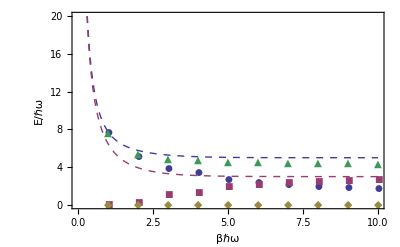

```mathematica
bead=2;
rhoType = 0;
permPlot=ListPlot[Table[Table[points[bead][i][rhoType][[j,2]],{j,1,Length[points[bead][i][rhoType]]}],{i,0,nperm}],PlotStyle->Thick,PlotMarkers-> Automatic];
Show[modelePlot,permPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["E/ℏω",Bold]}]
```

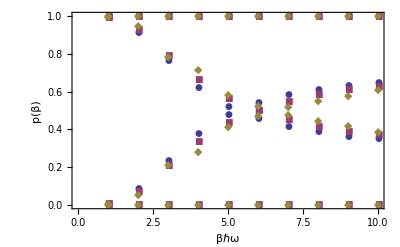

```mathematica
For[i=0,i<nperm+1,i++,For[j=0,j<nbeads,j++,prob[j][i]=Table[{points[j][i][rhoType][[l,1]],(points[j][i][rhoType][[l,2]])/(points[j][nperm][rhoType][[l,2]])},{l,1,Length[points[j][i][rhoType]]}]]]
probPlot=ListPlot[Table[Flatten[Table[prob[j][i],{i,0,nperm}],1],{j,0,nbeads-1}],PlotStyle->Thick,PlotMarkers-> Automatic];
Show[probPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["p(β)",Bold]}]
```

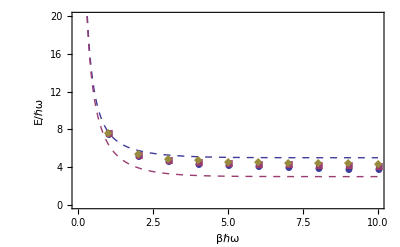

```mathematica
perm=3;
beadPlot=ListPlot[Table[Table[points[i][perm][rhoType][[j,2]],{j,1,Length[points[i][perm][rhoType]]}],{i,0,nbeads-1}],PlotStyle->Thick,PlotMarkers-> Automatic];
Show[modelePlot,beadPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["E/ℏω",Bold]}]
```

```mathematica
rhoType=1;
```

```mathematica
Clear[errorPoints]
```

```mathematica
modelePoints=Table[efunc,{β,1.0,nDataPoints}];
For[k=0,k≤ 1,k++,For[j=0,j<nbeads,j++,errorPoints[j][k]=Table[{i,(modelePoints[[i]]-points[j][nperm][k][[i,2]])/modelePoints[[i]]},{i,1,nDataPoints}]]]
```

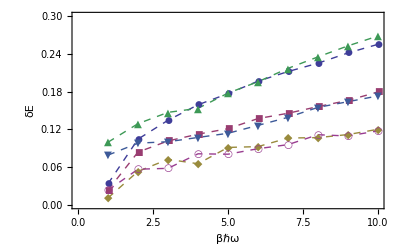

```mathematica
errPlot=ListPlot[Flatten[Table[Table[errorPoints[i][k],{i,0,nbeads-1}],{k,0,1}],1],PlotStyle->Dashed,PlotMarkers-> Automatic, PlotRange->{{0,nDataPoints},{0,0.3}},Joined-> True];
Show[errPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["δE",Bold]}]
```